### Input

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
T593= 0.951599 Flatten[Import["muB593/TMeV.dat"]];
msigma593= 0.951599 Flatten[Import["muB593/mSigma.dat"]];
mpion593= 0.951599 Flatten[Import["muB593/mPion.dat"]];

MsigmaofT593=Table[{T593[[n]],msigma593[[n]]},{n,1,Length[T593]}];
MpionofT593=Table[{T593[[n]],mpion593[[n]]},{n,1,Length[T593]}];
Mdiff593=Table[{T593[[n]],mpion593[[n]]-msigma593[[n]]},{n,1,Length[T593]}];
```

```mathematica
T592d5= 0.951599 Flatten[Import["muB592d5/TMeV.dat"]];
msigma592d5= 0.951599 Flatten[Import["muB592d5/mSigma.dat"]];
mpion592d5= 0.951599 Flatten[Import["muB592d5/mPion.dat"]];

MsigmaofT592d5=Table[{T592d5[[n]],msigma592d5[[n]]},{n,1,Length[T592d5]}];
MpionofT592d5=Table[{T592d5[[n]],mpion592d5[[n]]},{n,1,Length[T592d5]}];
Mdiff592d5=Table[{T592d5[[n]],mpion592d5[[n]]-msigma592d5[[n]]},{n,1,Length[T592d5]}];
```

```mathematica
T592= 0.951599 Flatten[Import["muB592/TMeV.dat"]];
msigma592= 0.951599 Flatten[Import["muB592/mSigma.dat"]];
mpion592= 0.951599 Flatten[Import["muB592/mPion.dat"]];

MsigmaofT592=Table[{T592[[n]],msigma592[[n]]},{n,1,Length[T592]}];
MpionofT592=Table[{T592[[n]],mpion592[[n]]},{n,1,Length[T592]}];
Mdiff592=Table[{T592[[n]],mpion592[[n]]-msigma592[[n]]},{n,1,Length[T592]}];
```

```mathematica
T591= 0.951599 Flatten[Import["muB591/TMeV.dat"]];
msigma591= 0.951599 Flatten[Import["muB591/mSigma.dat"]];
mpion591= 0.951599 Flatten[Import["muB591/mPion.dat"]];

MsigmaofT591=Table[{T591[[n]],msigma591[[n]]},{n,1,Length[T591]}];
MpionofT591=Table[{T591[[n]],mpion591[[n]]},{n,1,Length[T591]}];
Mdiff591=Table[{T591[[n]],mpion591[[n]]-msigma591[[n]]},{n,1,Length[T591]}];
```

```mathematica
T590= 0.951599 Flatten[Import["muB590/TMeV.dat"]];
msigma590= 0.951599 Flatten[Import["muB590/mSigma.dat"]];
mpion590= 0.951599 Flatten[Import["muB590/mPion.dat"]];

MsigmaofT590=Table[{T590[[n]],msigma590[[n]]},{n,1,Length[T590]}];
MpionofT590=Table[{T590[[n]],mpion590[[n]]},{n,1,Length[T590]}];
Mdiff590=Table[{T590[[n]],mpion590[[n]]-msigma590[[n]]},{n,1,Length[T590]}];
```

```mathematica
T580= 0.951599 Flatten[Import["muB580/TMeV.dat"]];
msigma580= 0.951599 Flatten[Import["muB580/mSigma.dat"]];
mpion580= 0.951599 Flatten[Import["muB580/mPion.dat"]];

MsigmaofT580=Table[{T580[[n]],msigma580[[n]]},{n,1,Length[T580]}];
MpionofT580=Table[{T580[[n]],mpion580[[n]]},{n,1,Length[T580]}];
Mdiff580=Table[{T580[[n]],mpion580[[n]]-msigma580[[n]]},{n,1,Length[T580]}];
```

```mathematica
T570= 0.951599 Flatten[Import["muB570/TMeV.dat"]];
msigma570= 0.951599 Flatten[Import["muB570/mSigma.dat"]];
mpion570= 0.951599 Flatten[Import["muB570/mPion.dat"]];

MsigmaofT570=Table[{T570[[n]],msigma570[[n]]},{n,1,Length[T570]}];
MpionofT570=Table[{T570[[n]],mpion570[[n]]},{n,1,Length[T570]}];
Mdiff570=Table[{T570[[n]],mpion570[[n]]-msigma570[[n]]},{n,1,Length[T570]}];
```

```mathematica
T560= 0.951599 Flatten[Import["muB560/TMeV.dat"]];
msigma560= 0.951599 Flatten[Import["muB560/mSigma.dat"]];
mpion560= 0.951599 Flatten[Import["muB560/mPion.dat"]];

MsigmaofT560=Table[{T560[[n]],msigma560[[n]]},{n,1,Length[T560]}];
MpionofT560=Table[{T560[[n]],mpion560[[n]]},{n,1,Length[T560]}];
Mdiff560=Table[{T560[[n]],mpion560[[n]]-msigma560[[n]]},{n,1,Length[T560]}];
```

### Evaluation

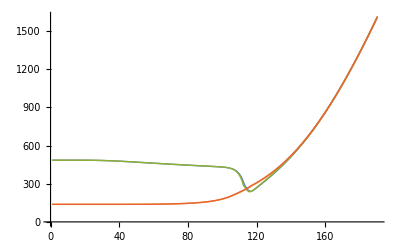

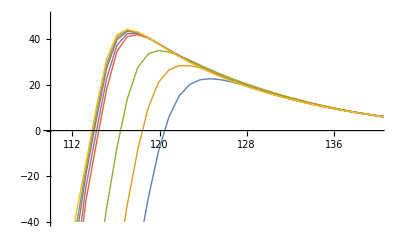

```mathematica
ListPlot[{MsigmaofT590,MpionofT590,MsigmaofT593,MpionofT593},Joined->True,PlotStyle->Thick]
ListPlot[{Mdiff560,Mdiff570,Mdiff580,Mdiff590,Mdiff591,Mdiff592,Mdiff592d5,Mdiff593},Joined->True,PlotStyle->Thick,PlotRange->{{110,140},{-40,50}}]
```

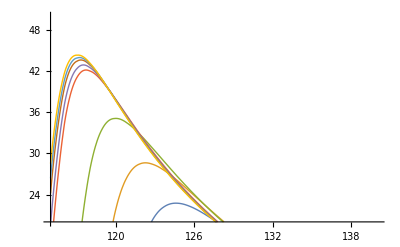

```mathematica
Plot[{Interpolation[Mdiff560][T],Interpolation[Mdiff570][T],Interpolation[Mdiff580][T],Interpolation[Mdiff590][T],Interpolation[Mdiff591][T],Interpolation[Mdiff592][T],Interpolation[Mdiff592d5][T],Interpolation[Mdiff593][T]},{T,115,140},PlotStyle->Thick,PlotRange->{{115,140},{20,50}}]
```

```mathematica
Peak560=FindMaximum[Interpolation[Mdiff560][T],{T,115,140}][[1]];TPeak560=T/.FindMaximum[Interpolation[Mdiff560][T],{T,115,140}][[2]];Peak570=FindMaximum[Interpolation[Mdiff570][T],{T,115,140}][[1]];
TPeak570=T/.FindMaximum[Interpolation[Mdiff570][T],{T,115,140}][[2]];Peak580=FindMaximum[Interpolation[Mdiff580][T],{T,115,140}][[1]];TPeak580=T/.FindMaximum[Interpolation[Mdiff580][T],{T,115,140}][[2]];Peak590=FindMaximum[Interpolation[Mdiff590][T],{T,115,140}][[1]];TPeak590=T/.FindMaximum[Interpolation[Mdiff590][T],{T,115,140}][[2]];Peak591=FindMaximum[Interpolation[Mdiff591][T],{T,115,140}][[1]];TPeak591=T/.FindMaximum[Interpolation[Mdiff591][T],{T,115,140}][[2]];Peak592=FindMaximum[Interpolation[Mdiff592][T],{T,115,140}][[1]];TPeak592=T/.FindMaximum[Interpolation[Mdiff592][T],{T,115,140}][[2]];Peak592d5=FindMaximum[Interpolation[Mdiff592d5][T],{T,115,140}][[1]];
TPeak592d5=T/.FindMaximum[Interpolation[Mdiff592d5][T],{T,115,140}][[2]];Peak593=FindMaximum[Interpolation[Mdiff593][T],{T,115,140}][[1]];TPeak593=T/.FindMaximum[Interpolation[Mdiff593][T],{T,115,140}][[2]];
```

```mathematica
TPeak560
```

124.576

```mathematica
dataΔm=Table[{{560,Peak560},{570,Peak570},{580,Peak580},{590,Peak590},{591,Peak591},{592,Peak592},{592.5,Peak592d5},{593,Peak593}}];
dataΔmshort=Table[{{590,Peak590},{591,Peak591},{592,Peak592},{592.5,Peak592d5},{593,Peak593}}];
dataT=Table[{{560,TPeak560},{570,TPeak570},{580,TPeak580},{590,TPeak590},{591,TPeak591},{592,TPeak592},{592.5,TPeak592d5},{593,TPeak593}}];
dataTshort=Table[{{590,TPeak590},{591,TPeak591},{592,TPeak592},{592.5,TPeak592d5},{593,TPeak593}}];

datamσ=Table[{{560,Interpolation[msigma560][TPeak560]},{570,Interpolation[msigma570][TPeak570]},{580,Interpolation[msigma580][TPeak580]},{590,Interpolation[msigma590][TPeak590]},{591,Interpolation[msigma591][TPeak591]},{592,Interpolation[msigma592][TPeak592]},{592.5,Interpolation[msigma592d5][TPeak592d5]},{593,Interpolation[msigma593][TPeak593]}}];
```

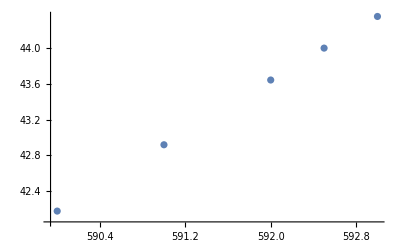

```mathematica
ListPlot[dataΔmshort]
```

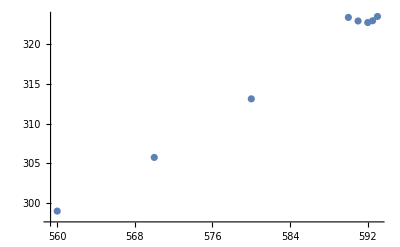

```mathematica
ListPlot[datamσ]
```

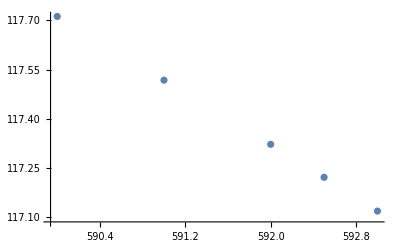

```mathematica
ListPlot[dataTshort]
```

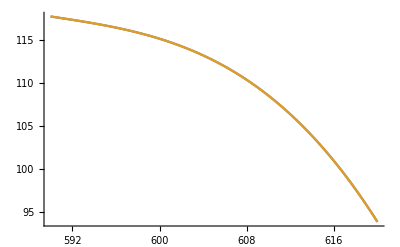

```mathematica
Plot[{Interpolation[dataTshort][μ],Interpolation[dataT][μ]},{μ,590,620},PlotRange->All]
```

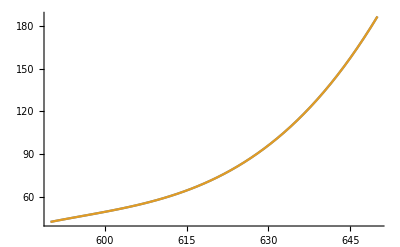

```mathematica
Plot[{Interpolation[dataΔmshort][μ],Interpolation[dataΔmshort][μ]},{μ,590,650},PlotRange->All]
```

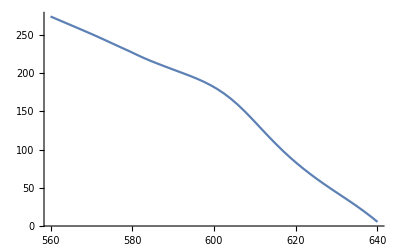

```mathematica
Plot[{Interpolation[mpion593][Interpolation[dataT][μ]]-Interpolation[dataΔm][μ]},{μ,560,640},PlotRange->All]
```

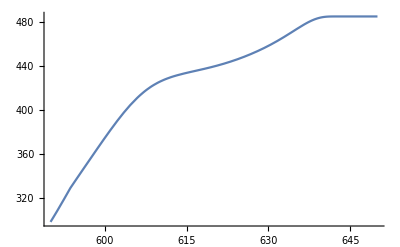

```mathematica
Plot[{Interpolation[msigma593][Interpolation[dataTshort][μ]]},{μ,590,650},PlotRange->All]
```

```mathematica
620*.9515
```

589.93